Question5

```mathematica
Clear[T, t, myPower, rect]
myPower[X_, range_, limit_]:= Limit[1/(2*T)*Integrate[(X)^2, range],T->limit]
rect[t_] := UnitStep[t + 0.5] - UnitStep[t - 0.5]
```

```mathematica
Clear[T, t, myEnergy]
myEnergy[X_, range_] := Integrate[(X)^2, range]
```

```mathematica
Clear[x1, t, A, a, T]
x1[t_] = A*E^(-a*t)
Integrate[(x1[t])^2, {t, 0, Infinity}, Assumptions->(Re[a] > 0)]
Limit[(1/(2*T))*Integrate[(x1[t])^2, {t, 0, Infinity}, Assumptions->(Re[a] > 0)], T->Infinity]
```

A ⅇ^(-a t)

A^2/(2 a)

0

```mathematica
Clear[x2, t, A, w, o]
x2[t_] = A*Cos[w*t + o]
Integrate[(x2[t])^2, {t, -Infinity, Infinity}]
Limit[1/(2*T)*Integrate[(x2[t])^2, {t, -T, T}],T->Infinity]
```

A Cos[o+t w]

Integrate::idiv: Integral of A^2 Cos[o+t w]^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ A^2 Cos[o+t w]^2ⅆt

ConditionalExpression[A^2/2, w∈ℝ]

```mathematica
Clear[x3, t]
x3[t_] = 1 / (t)^(0.25)
Integrate[Abs[x3[t]]^2, {t, 3, Infinity}]
Limit[1/(2*T)*Integrate[x3[t]^2, {t, 3, T}], T->Infinity]
```

1/t^0.25

Integrate::idiv: Integral of 1/t^0.5 does not converge on {3,∞}.

∫_3^∞ 1/Abs[t]^0.5 ⅆt

0.

```mathematica
Clear[x4, t]
x4[t_] = t*E^(-2t)
Integrate[Abs[x4[t]]^2, {t, 0, Infinity}]
Limit[1/(2*T)*Integrate[Abs[x4[t]]^2, {t, 0, Infinity}], T->Infinity]
```

ⅇ^(-2 t) t

1/32

0

```mathematica
Clear[x5, t]
x5[t_] = E^(-2t) * Cos[0.5*Pi*t]
Integrate[Abs[x5[t]]^2, {t, 0, Infinity}]
Limit[1/(2*T)*Integrate[Abs[x5[t]]^2, {t, 0, Infinity}], T->Infinity]
```

ⅇ^(-2 t) Cos[1.5708 t]

0.202311

0.

Sinc[(π t)/3]-Sinc[(π t)/3] (-UnitStep[-0.5+Sinc[(π t)/3]]+UnitStep[0.5+Sinc[(π t)/3]])

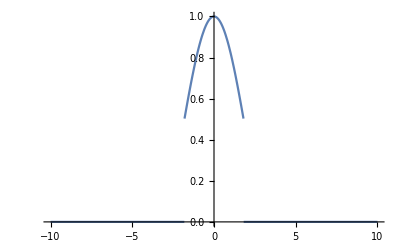

```mathematica
y[t_] = Sinc[Pi*t / 3] - (rect[Sinc[Pi*t/3]] * Sinc[Pi*t/3]) 
Plot[y[t], {t, -10, 10}]
```

```mathematica
FindRoot[Sinc[Pi * t / 3] - 0.5 == 0, {t, 1}]
```

{t→1.81006}

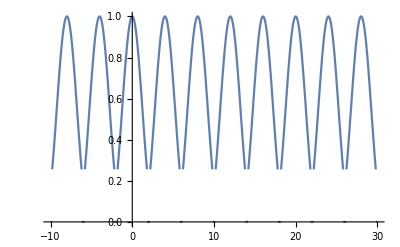

```mathematica
Clear[x6, t]
x6[t_] = ∑_(k=-10)^10 (y[t - 4k])^2
Plot[x6[t], {t, -10, 30}]
```